# List

## Creating lists

```mathematica
Table[ 2j ,{i,0,4},{j,0,i}]
Table[Range[0,j,2],{j,Range[0,8,2]}]
```

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

2. Create a ten - element list of random 1 s, 0 s and - 1 s.

```mathematica
2RandomInteger[1,{10}]-1
```

```mathematica
{1,1,1,-1,-1,-1,-1,-1,1,-1}
```

4. Generate a Array[f,5] list using Table.

```mathematica
Table[f[k],{k,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
ClearAll[f]
Table[f[i,j],{i,3},{j,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

```mathematica
Table[{i,j},{j,{-1,0,1}},{i,{-2,2}}]
Table[{k,l},{k,{-2,-1,0,1,2}},{l,{-1,1}}]
```

{{{-2,-1},{2,-1}},{{-2,0},{2,0}},{{-2,1},{2,1}}}

{{{-2,-1},{-2,1}},{{-1,-1},{-1,1}},{{0,-1},{0,1}},{{1,-1},{1,1}},{{2,-1},{2,1}}}

## The structure of the list

#### Testing a list

```mathematica
Position,Count,MemberQ,FreeQ
```

#### Measuring list

```mathematica
{Length,Dimensions,MatrixForm,ArrayDepth,TreeForm}
```

#### Exercises

1. Given the list of integers such as the  following, count the number of zeros. Find a way to count all those elements of the list which are not ones.

```mathematica
ints=RandomInteger[{-5,5},30];
List @ ints //Grid[#,Dividers->All]&
{Count[ints,0],Length[ints]-Count[ints,0]}
```

-4 | -3 | -1 | 5 | 1 | 5 | -4 | -1 | -4 | -3 | -1 | 5 | 4 | -1 | 3 | 3 | 2 | 0 | -4 | 1 | 4 | 0 | -1 | -5 | 3 | 2 | 4 | 0 | 0 | -2

{4,26}

```mathematica
ints
```

{-4,-3,-1,5,1,5,-4,-1,-4,-3,-1,5,4,-1,3,3,2,0,-4,1,4,0,-1,-5,3,2,4,0,0,-2}

2. Determine dimensions of the list.

{2,3,2}

4

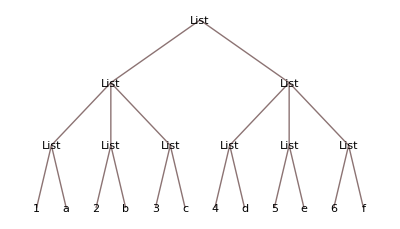

```mathematica
l={{{1,a},{2,b},{3,c}},{{4,d},{5,e},{6,f}}};
Dimensions @ l
Depth @ l
TreeForm @ l
```

{{2,1},{4,3}}

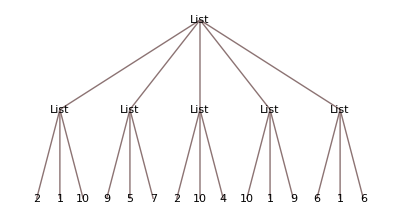

```mathematica
l={{2, 1, 10}, {9, 5, 7}, {2, 10, 4}, {10, 1, 9}, {6, 1, 6}};
Position[l,9]
TreeForm[l]
```

```mathematica
Depth [l]
```

3

## 3.3 Operations on lists

#### Extracting elements

```mathematica
(* 
 Part
Take
*)
ClearAll[a,z]
z=Table[Subscript[a, i,j],{i,3},{j,5}];
z //MatrixForm
z⟦;;2,;;3⟧ 
Take[z,2,3]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5))

{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)}}

{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)}}

```mathematica
MatrixForm @ SortBy[#,Last]& @  z
```

```mathematica
({{Subscript[a, 1,1], Subscript[a, 1,2], Subscript[a, 1,3], Subscript[a, 1,4], Subscript[a, 1,5]}, {Subscript[a, 2,1], Subscript[a, 2,2], Subscript[a, 2,3], Subscript[a, 2,4], Subscript[a, 2,5]}, {Subscript[a, 3,1], Subscript[a, 3,2], Subscript[a, 3,3], Subscript[a, 3,4], Subscript[a, 3,5]}})
```

```mathematica
ClearAll[l]
l=Range[50]
Partition[l, 2]//Flatten
Partition[l, 2,1] //Flatten //Sort
```

{1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,11,11,12,12,13,13,14,14,15,15,16,16,17,17,18,18,19,19,20,20,21,21,22,22,23,23,24,24,25,25,26,26,27,27,28,28,29,29,30,30,31,31,32,32,33,33,34,34,35,35,36,36,37,37,38,38,39,39,40,40,41,41,42,42,43,43,44,44,45,45,46,46,47,47,48,48,49,49,50}

#### Exercises

```mathematica
{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}//Transpose
```

{{x1,x2,x3,x4},{y1,y2,y3,y4}}

2. Two-dimensional random walk on a square lattice.

```mathematica
steps={{1, 0}, {0, 1}, {-1, 0}, {0, -1}}
```

{{1,0},{0,1},{-1,0},{0,-1}}

```mathematica
RandomInteger[{1,4},20]
```

```mathematica
Table[#,10]&@ 
steps⟦RandomInteger[{1,4}]⟧
```

{{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

3. Extract elements in the even - numbered locations in the list.

```mathematica
l={a,b,c,d,e,f,g,h,i,j,k};
Flatten@ Partition[l,1,2]
l⟦Range[1,11,2]⟧
```

{a,c,e,g,i,k}

{a,c,e,g,i,k}

4. Given a matrix, use list component assignment to swap any two rows.

```mathematica
mat=Table[Subscript[m, i,j],{i,1,5},{j,1,5}];
MatrixForm@ mat
{mat⟦2,All⟧,mat⟦3,All⟧} ={mat⟦3,All⟧,mat⟦2,All⟧};
MatrixForm@ mat
```

(m_(1,1) | m_(1,2) | m_(1,3) | m_(1,4) | m_(1,5)
m_(2,1) | m_(2,2) | m_(2,3) | m_(2,4) | m_(2,5)
m_(3,1) | m_(3,2) | m_(3,3) | m_(3,4) | m_(3,5)
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4) | m_(4,5)
m_(5,1) | m_(5,2) | m_(5,3) | m_(5,4) | m_(5,5))

(m_(1,1) | m_(1,2) | m_(1,3) | m_(1,4) | m_(1,5)
m_(3,1) | m_(3,2) | m_(3,3) | m_(3,4) | m_(3,5)
m_(2,1) | m_(2,2) | m_(2,3) | m_(2,4) | m_(2,5)
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4) | m_(4,5)
m_(5,1) | m_(5,2) | m_(5,3) | m_(5,4) | m_(5,5))

5. Create a function AddColumn[mat, col, pos] that inserts a column vector col into matrix mat at the column position given by pos.

```mathematica
ClearAll[a,b,c,d];
addColumn[mat_,col_,pos_]:=
mat //Transpose // Insert[#,col,pos]& //Transpose
mat=RandomInteger[9,{4,4}];
mat // MatrixForm

addColumn[mat,{a,b,c,d},2] //MatrixForm //Print
```

(0 | 8 | 7 | 4
4 | 7 | 7 | 8
1 | 5 | 3 | 7
6 | 6 | 2 | 3)

(0 | a | 8 | 7 | 4
4 | b | 7 | 7 | 8
1 | c | 5 | 3 | 7
6 | d | 6 | 2 | 3)

6.